# BeamSolver usage examples

```mathematica
<<BeamSolver`
```

## Simple benchmark beams

## 1 Simply supported beam with a central point load

### 1 Problem setup

```mathematica
ClearAll[L,EE,J,P,x];
```

```mathematica
beam1=<|"Supports"->{<|"Type"->"Pin","x"->0|>,<|"Type"->"Pin","x"->L|>},"Loadings"->{<|"Type"->"Force","x"->L/2,"Value"->-P|>},"Length"->L,"E"->EE,"J"->J,"Numbers"->{L->4,EE->210 10^9,J->8 10^-6,P->10 10^3}|>;
```

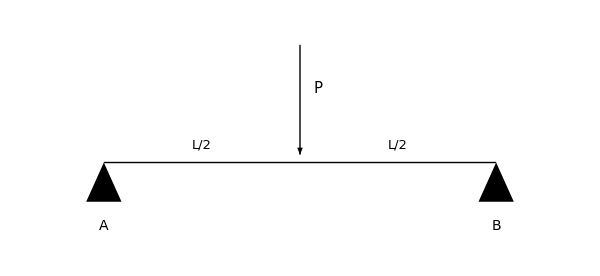

```mathematica
beamScheme1=With[{Ln=L/. beam1["Numbers"]},Graphics[{Thick,(*Beam*)Line[{{0,0},{Ln,0}}],(*Left pin support*)Polygon[{{-0.18,-0.4},{0.18,-0.4},{0,0}}],(*Right support*)Polygon[{{Ln-0.18,-0.4},{Ln+0.18,-0.4},{Ln,0}}],(*Central point load*)Arrow[{{Ln/2,1.2},{Ln/2,0.08}}],Text[Style["P",15,Italic],{Ln/2+0.18,0.75}],Text[Style["A",14,Italic],{0,-0.65}],Text[Style["B",14,Italic],{Ln,-0.65}],Text[Style["L/2",13],{Ln/4,0.18}],Text[Style["L/2",13],{3 Ln/4,0.18}]},PlotRange->{{-0.5,Ln+0.5},{-0.9,1.4}},ImageSize->600]]
```

### 2 Theoretical solutions

```mathematica
theoreticalValues1=<|"ReactionA"->P/2,"ReactionB"->P/2,"MaximumBendingMoment"->P L/4,"MaximumBendingMomentPosition"->L/2,"MaximumDeflection"->-P L^3/(48 EE J),"MaximumDeflectionPosition"->L/2|>;
```

```mathematica
theoreticalValues1Numerical=N[theoreticalValues1/.
beam1["Numbers"]]
```

<|ReactionA→5000.,ReactionB→5000.,MaximumBendingMoment→10000.,MaximumBendingMomentPosition→2.,MaximumDeflection→-0.00793651,MaximumDeflectionPosition→2.|>

### 3 BeamSolver solution

Purely analytical solution

```mathematica
beam1Solved=beamSolve[beam1]
```

<|Supports→{<|Type→Pin,x→0|>,<|Type→Pin,x→L|>},Loadings→{<|Type→Force,x→L/2,Value→-P|>,<|Type→Force,x→0,Value→P/2,Kind→Reaction|>,<|Type→Force,x→L,Value→P/2,Kind→Reaction|>},Length→L,E→EE,J→J,Boundary conditions→{BeamSolver`Private`y''[0]==0,BeamSolver`Private`y''[L]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y[L]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==-2 P DiracDelta[L-2 BeamSolver`Private`x]+1/2 P DiracDelta[BeamSolver`Private`x]+1/2 P DiracDelta[-L+BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},1/2 (-P UnitStep[-L]+P UnitStep[-L/2]+P UnitStep[L/2]-P UnitStep[L])+1/2 P UnitStep[BeamSolver`Private`x1$]+1/2 P UnitStep[-L+BeamSolver`Private`x1$]-P UnitStep[-L/2+BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},1/2 (L P UnitStep[-L]-L P UnitStep[-L/2])+1/2 BeamSolver`Private`x1$ (-P UnitStep[-L]+P UnitStep[-L/2]+P UnitStep[L/2]-P UnitStep[L])+1/2 P BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]+1/2 P (-L+BeamSolver`Private`x1$) UnitStep[-L+BeamSolver`Private`x1$]-P (-L/2+BeamSolver`Private`x1$) UnitStep[-L/2+BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/(EE J)(1/2 BeamSolver`Private`x1$ (L P UnitStep[-L]-L P UnitStep[-L/2])+1/16 (-4 L^2 P UnitStep[-L]+3 L^2 P UnitStep[-L/2]-L^2 P UnitStep[L/2])+1/4 (BeamSolver`Private`x1$)^2 (-P UnitStep[-L]+P UnitStep[-L/2]+P UnitStep[L/2]-P UnitStep[L])+1/4 P (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]+1/4 P (-L+BeamSolver`Private`x1$)^2 UnitStep[-L+BeamSolver`Private`x1$]-1/2 P (-L/2+BeamSolver`Private`x1$)^2 UnitStep[-L/2+BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/(EE J)(1/4 (BeamSolver`Private`x1$)^2 (L P UnitStep[-L]-L P UnitStep[-L/2])+1/48 (4 L^3 P UnitStep[-L]-L^3 P UnitStep[-L/2])+1/16 BeamSolver`Private`x1$ (-4 L^2 P UnitStep[-L]+3 L^2 P UnitStep[-L/2]-L^2 P UnitStep[L/2])+1/12 (BeamSolver`Private`x1$)^3 (-P UnitStep[-L]+P UnitStep[-L/2]+P UnitStep[L/2]-P UnitStep[L])+1/12 P (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$]+1/12 P (-L+BeamSolver`Private`x1$)^3 UnitStep[-L+BeamSolver`Private`x1$]-1/6 P (-L/2+BeamSolver`Private`x1$)^3 UnitStep[-L/2+BeamSolver`Private`x1$])]|>,Numbers→{L→4,EE→210000000000,J→1/125000,P→10000}|>

With numbers:

```mathematica
beam1SolvedValues=beamPutValues[beam1Solved]
```

<|Supports→{<|Type→Pin,x→0|>,<|Type→Pin,x→4|>},Loadings→{<|Type→Force,x→2,Value→-10000|>,<|Type→Force,x→0,Value→5000,Kind→Reaction|>,<|Type→Force,x→4,Value→5000,Kind→Reaction|>},Length→4,E→210000000000,J→1/125000,Boundary conditions→{BeamSolver`Private`y''[0]==0,BeamSolver`Private`y''[4]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y[4]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==5000 DiracDelta[-4+BeamSolver`Private`x]-10000 DiracDelta[-2+BeamSolver`Private`x]+5000 DiracDelta[BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},5000 UnitStep[-4+BeamSolver`Private`x1$]-10000 UnitStep[-2+BeamSolver`Private`x1$]+5000 UnitStep[BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},5000 (-4+BeamSolver`Private`x1$) UnitStep[-4+BeamSolver`Private`x1$]-10000 (-2+BeamSolver`Private`x1$) UnitStep[-2+BeamSolver`Private`x1$]+5000 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/1680000(-10000+2500 (-4+BeamSolver`Private`x1$)^2 UnitStep[-4+BeamSolver`Private`x1$]-5000 (-2+BeamSolver`Private`x1$)^2 UnitStep[-2+BeamSolver`Private`x1$]+2500 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/1680000(-10000 BeamSolver`Private`x1$+2500/3 (-4+BeamSolver`Private`x1$)^3 UnitStep[-4+BeamSolver`Private`x1$]-5000/3 (-2+BeamSolver`Private`x1$)^3 UnitStep[-2+BeamSolver`Private`x1$]+2500/3 (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$])]|>|>

```mathematica
solverValues1=<|"ReactionA"->beamReactions[beam1SolvedValues][[1]]["Value"],"ReactionB"->beamReactions[beam1SolvedValues][[2]]["Value"],"MaximumBendingMoment"->beamMaxValue[beam1SolvedValues,"BendingMoment"]["Value"],"MaximumBendingMomentPosition"->beamMaxValue[beam1SolvedValues,"BendingMoment"]["Position"],"MaximumDeflection"->beamMaxValue[beam1SolvedValues,"Deflection"]["Value"],"MaximumDeflectionPosition"->beamMaxValue[beam1SolvedValues,"Deflection"]["Position"]|>
```

<|ReactionA→5000,ReactionB→5000,MaximumBendingMoment→10000.,MaximumBendingMomentPosition→2,MaximumDeflection→-0.00793651,MaximumDeflectionPosition→2|>

Diagrams:

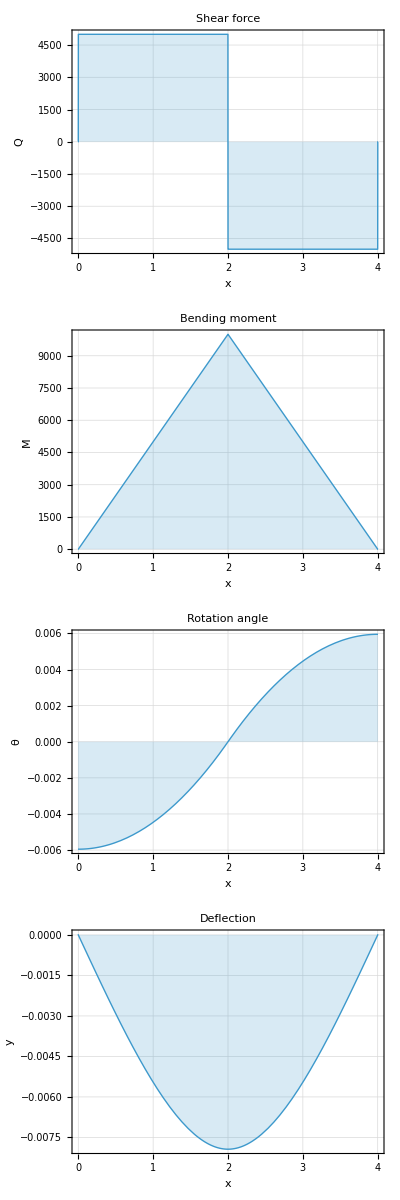

```mathematica
beamPlots[beam1SolvedValues]
```

## 2 Simply supported beam with a uniformly distributed load

### 1 Problem setup

```mathematica
ClearAll[L,EE,J,q,x];

beam2=<|"Supports"->{<|"Type"->"Pin","x"->0|>,<|"Type"->"Pin","x"->L|>},"Loadings"->{<|"Type"->"Distributed","x begin"->0,"x end"->L,"Value"->-q|>},"Length"->L,"E"->EE,"J"->J,"Numbers"->{L->4,EE->210 10^9,J->8 10^-6,q->5  10^3}|>;
```

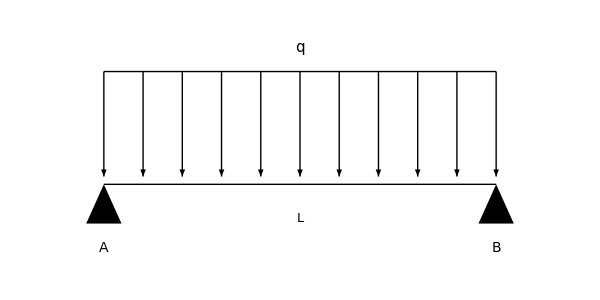

```mathematica
beamScheme2=With[{Ln=L/. beam2["Numbers"]},Graphics[{Thick,(*Beam*)Line[{{0,0},{Ln,0}}],(*Supports*)Polygon[{{-0.18,-0.4},{0.18,-0.4},{0,0}}],Polygon[{{Ln-0.18,-0.4},{Ln+0.18,-0.4},{Ln,0}}],(*Distributed-load line*)Line[{{0,1.15},{Ln,1.15}}],(*Distributed-load arrows*)Table[Arrow[{{xi,1.15},{xi,0.08}}],{xi,0,Ln,Ln/10}],(*Labels*)Text[Style["q",15,Italic],{Ln/2,1.4}],Text[Style["A",14,Italic],{0,-0.65}],Text[Style["B",14,Italic],{Ln,-0.65}],Text[Style["L",13],{Ln/2,-0.35}]},PlotRange->{{-0.5,Ln+0.5},{-0.9,1.6}},ImageSize->600]]
```

### 2 Theoretical solutions

```mathematica
theoreticalValues2=<|"ReactionA"->q L/2,"ReactionB"->q L/2,"MaximumBendingMoment"->q L^2/8,"MaximumBendingMomentPosition"->L/2,"MaximumDeflection"->-5 q L^4/(384 EE J),"MaximumDeflectionPosition"->L/2|>;
```

```mathematica
theoreticalValues2Numerical=N[theoreticalValues2/.
beam2["Numbers"]]
```

<|ReactionA→10000.,ReactionB→10000.,MaximumBendingMoment→10000.,MaximumBendingMomentPosition→2.,MaximumDeflection→-0.00992063,MaximumDeflectionPosition→2.|>

### 3 BeamSolver solution

Purely analytical solution

```mathematica
beam2Solved=beamSolve[beam2]
```

<|Supports→{<|Type→Pin,x→0|>,<|Type→Pin,x→L|>},Loadings→{<|Type→Distributed,x begin→0,x end→L,Value→-q|>,<|Type→Force,x→0,Value→(L q)/2,Kind→Reaction|>,<|Type→Force,x→L,Value→(L q)/2,Kind→Reaction|>},Length→L,E→EE,J→J,Boundary conditions→{BeamSolver`Private`y''[0]==0,BeamSolver`Private`y''[L]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y[L]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==1/2 L q DiracDelta[BeamSolver`Private`x]+1/2 L q DiracDelta[-L+BeamSolver`Private`x]-q HeavisideTheta[BeamSolver`Private`x]+q HeavisideTheta[-L+BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},1/2 L q UnitStep[BeamSolver`Private`x1$]-q BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]+1/2 L q UnitStep[-L+BeamSolver`Private`x1$]+q (-L+BeamSolver`Private`x1$) UnitStep[-L+BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},1/2 L q BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]-1/2 q (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]+1/2 L q (-L+BeamSolver`Private`x1$) UnitStep[-L+BeamSolver`Private`x1$]+1/2 q (-L+BeamSolver`Private`x1$)^2 UnitStep[-L+BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/(EE J)(1/24 (-L^3 q UnitStep[-L]-L^3 q UnitStep[L])+1/4 L q (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]-1/6 q (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$]+1/4 L q (-L+BeamSolver`Private`x1$)^2 UnitStep[-L+BeamSolver`Private`x1$]+1/6 q (-L+BeamSolver`Private`x1$)^3 UnitStep[-L+BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/(EE J)(1/24 L^4 q UnitStep[-L]+1/24 BeamSolver`Private`x1$ (-L^3 q UnitStep[-L]-L^3 q UnitStep[L])+1/12 L q (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$]-1/24 q (BeamSolver`Private`x1$)^4 UnitStep[BeamSolver`Private`x1$]+1/12 L q (-L+BeamSolver`Private`x1$)^3 UnitStep[-L+BeamSolver`Private`x1$]+1/24 q (-L+BeamSolver`Private`x1$)^4 UnitStep[-L+BeamSolver`Private`x1$])]|>,Numbers→{L→4,EE→210000000000,J→1/125000,q→5000}|>

With numbers:

```mathematica
beam2SolvedValues=beamPutValues[beam2Solved]
```

<|Supports→{<|Type→Pin,x→0|>,<|Type→Pin,x→4|>},Loadings→{<|Type→Distributed,x begin→0,x end→4,Value→-5000|>,<|Type→Force,x→0,Value→10000,Kind→Reaction|>,<|Type→Force,x→4,Value→10000,Kind→Reaction|>},Length→4,E→210000000000,J→1/125000,Boundary conditions→{BeamSolver`Private`y''[0]==0,BeamSolver`Private`y''[4]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y[4]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==10000 DiracDelta[-4+BeamSolver`Private`x]+10000 DiracDelta[BeamSolver`Private`x]+5000 HeavisideTheta[-4+BeamSolver`Private`x]-5000 HeavisideTheta[BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},10000 UnitStep[-4+BeamSolver`Private`x1$]+5000 (-4+BeamSolver`Private`x1$) UnitStep[-4+BeamSolver`Private`x1$]+10000 UnitStep[BeamSolver`Private`x1$]-5000 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},10000 (-4+BeamSolver`Private`x1$) UnitStep[-4+BeamSolver`Private`x1$]+2500 (-4+BeamSolver`Private`x1$)^2 UnitStep[-4+BeamSolver`Private`x1$]+10000 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]-2500 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/1680000(-40000/3+5000 (-4+BeamSolver`Private`x1$)^2 UnitStep[-4+BeamSolver`Private`x1$]+2500/3 (-4+BeamSolver`Private`x1$)^3 UnitStep[-4+BeamSolver`Private`x1$]+5000 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]-2500/3 (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/1680000(-(40000 BeamSolver`Private`x1$)/3+5000/3 (-4+BeamSolver`Private`x1$)^3 UnitStep[-4+BeamSolver`Private`x1$]+625/3 (-4+BeamSolver`Private`x1$)^4 UnitStep[-4+BeamSolver`Private`x1$]+5000/3 (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$]-625/3 (BeamSolver`Private`x1$)^4 UnitStep[BeamSolver`Private`x1$])]|>|>

```mathematica
solverValues2=<|"ReactionA"->beamReactions[beam2SolvedValues][[1]]["Value"],"ReactionB"->beamReactions[beam2SolvedValues][[2]]["Value"],"MaximumBendingMoment"->beamMaxValue[beam2SolvedValues,"BendingMoment"]["Value"],"MaximumBendingMomentPosition"->beamMaxValue[beam2SolvedValues,"BendingMoment"]["Position"],"MaximumDeflection"->beamMaxValue[beam2SolvedValues,"Deflection"]["Value"],"MaximumDeflectionPosition"->beamMaxValue[beam2SolvedValues,"Deflection"]["Position"]|>
```

<|ReactionA→10000,ReactionB→10000,MaximumBendingMoment→10000.,MaximumBendingMomentPosition→2.,MaximumDeflection→-0.00992063,MaximumDeflectionPosition→2.|>

Diagrams:

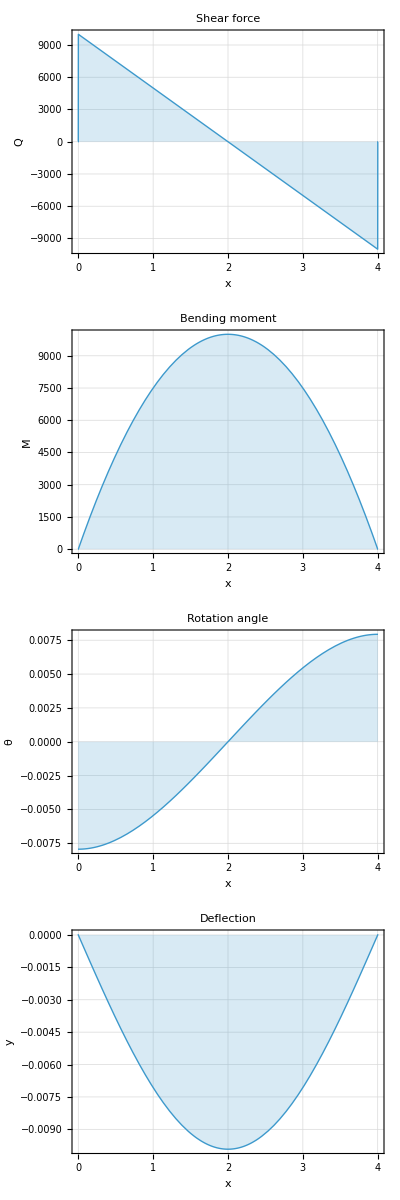

```mathematica
beamPlots[beam2SolvedValues]
```

## 3 Cantilever beam with a tip point load

### 1 Problem setup

```mathematica
ClearAll[L,EE,J,P,x];

beam3=<|"Supports"->{<|"Type"->"FixedEnd","x"->0|>},"Loadings"->{<|"Type"->"Force","x"->L,"Value"->-P|>},"Length"->L,"E"->EE,"J"->J,"Numbers"->{L->4,EE->210 10^9,J->8 10^-6,P->10 10^3}|>;
```

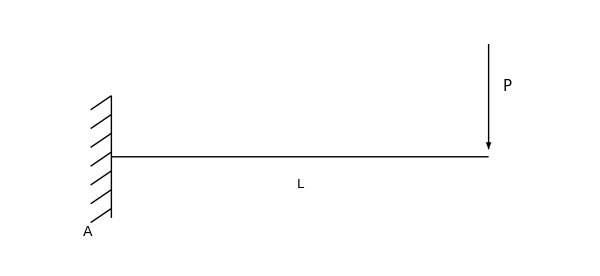

```mathematica
beamScheme3=With[{Ln=L/. beam3["Numbers"]},Graphics[{Thick,(*Beam*)Line[{{0,0},{Ln,0}}],(*Fixed support*)Line[{{0,-0.65},{0,0.65}}],Table[Line[{{-0.22,yi-0.15},{0,yi}}],{yi,-0.55,0.65,0.2}],(*Tip load*)Arrow[{{Ln,1.2},{Ln,0.08}}],(*Labels*)Text[Style["P",15,Italic],{Ln+0.2,0.75}],Text[Style["A",14,Italic],{-0.25,-0.8}],Text[Style["L",13],{Ln/2,-0.3}]},PlotRange->{{-0.6,Ln+0.6},{-1.0,1.4}},ImageSize->600]]
```

### 2 Theoretical solutions

```mathematica
theoreticalValues3=<|"ReactionForce"->P,"ReactionMoment"->P L,"MaximumBendingMoment"->-P L,"MaximumBendingMomentPosition"->0,"MaximumDeflection"->-P L^3/(3 EE J),"MaximumDeflectionPosition"->L|>;
```

```mathematica
theoreticalValues3Numerical=N[theoreticalValues3/.
beam3["Numbers"]]
```

<|ReactionForce→10000.,ReactionMoment→40000.,MaximumBendingMoment→-40000.,MaximumBendingMomentPosition→0.,MaximumDeflection→-0.126984,MaximumDeflectionPosition→4.|>

### 3 BeamSolver solution

Purely analytical solution

```mathematica
beam3Solved=beamSolve[beam3]
```

<|Supports→{<|Type→FixedEnd,x→0|>},Loadings→{<|Type→Force,x→L,Value→-P|>,<|Type→Force,x→0,Value→P,Kind→Reaction|>,<|Type→Moment,x→0,Value→L P,Kind→Reaction|>},Length→L,E→EE,J→J,Boundary conditions→{BeamSolver`Private`y''[0]==-L P,BeamSolver`Private`y''[L]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y'[0]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==P DiracDelta[BeamSolver`Private`x]-P DiracDelta[-L+BeamSolver`Private`x]-L P DiracDelta'[BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},P UnitStep[-L]+P UnitStep[BeamSolver`Private`x1$]-P UnitStep[-L+BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},-L P UnitStep[-L]+P BeamSolver`Private`x1$ UnitStep[-L]-L P UnitStep[BeamSolver`Private`x1$]+P BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]-P (-L+BeamSolver`Private`x1$) UnitStep[-L+BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/(EE J)(1/2 L^2 P UnitStep[-L]-L P BeamSolver`Private`x1$ UnitStep[-L]+1/2 P (BeamSolver`Private`x1$)^2 UnitStep[-L]-L P BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]+1/2 P (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]-1/2 P (-L+BeamSolver`Private`x1$)^2 UnitStep[-L+BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/(EE J)(-1/6 L^3 P UnitStep[-L]+1/2 L^2 P BeamSolver`Private`x1$ UnitStep[-L]-1/2 L P (BeamSolver`Private`x1$)^2 UnitStep[-L]+1/6 P (BeamSolver`Private`x1$)^3 UnitStep[-L]-1/2 L P (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]+1/6 P (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$]-1/6 P (-L+BeamSolver`Private`x1$)^3 UnitStep[-L+BeamSolver`Private`x1$])]|>,Numbers→{L→4,EE→210000000000,J→1/125000,P→10000}|>

With numbers:

```mathematica
beam3SolvedValues=beamPutValues[beam3Solved]
```

<|Supports→{<|Type→FixedEnd,x→0|>},Loadings→{<|Type→Force,x→4,Value→-10000|>,<|Type→Force,x→0,Value→10000,Kind→Reaction|>,<|Type→Moment,x→0,Value→40000,Kind→Reaction|>},Length→4,E→210000000000,J→1/125000,Boundary conditions→{BeamSolver`Private`y''[0]==-40000,BeamSolver`Private`y''[4]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y'[0]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==-10000 DiracDelta[-4+BeamSolver`Private`x]+10000 DiracDelta[BeamSolver`Private`x]-40000 DiracDelta'[BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},-10000 UnitStep[-4+BeamSolver`Private`x1$]+10000 UnitStep[BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},-10000 (-4+BeamSolver`Private`x1$) UnitStep[-4+BeamSolver`Private`x1$]-40000 UnitStep[BeamSolver`Private`x1$]+10000 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/1680000(-5000 (-4+BeamSolver`Private`x1$)^2 UnitStep[-4+BeamSolver`Private`x1$]-40000 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]+5000 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/1680000(-5000/3 (-4+BeamSolver`Private`x1$)^3 UnitStep[-4+BeamSolver`Private`x1$]-20000 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]+5000/3 (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$])]|>|>

```mathematica
solverValues3=<|"ReactionForce"->beamReactions[beam3SolvedValues][[1]]["Value"],"ReactionMoment"->beamReactions[beam3SolvedValues][[2]]["Value"],"MaximumBendingMoment"->beamMaxValue[beam3SolvedValues,"BendingMoment"]["Value"],"MaximumBendingMomentPosition"->beamMaxValue[beam3SolvedValues,"BendingMoment"]["Position"],"MaximumDeflection"->beamMaxValue[beam3SolvedValues,"Deflection"]["Value"],"MaximumDeflectionPosition"->beamMaxValue[beam3SolvedValues,"Deflection"]["Position"]|>
```

<|ReactionForce→10000,ReactionMoment→40000,MaximumBendingMoment→-40000.,MaximumBendingMomentPosition→0,MaximumDeflection→-0.126984,MaximumDeflectionPosition→4|>

Diagrams:

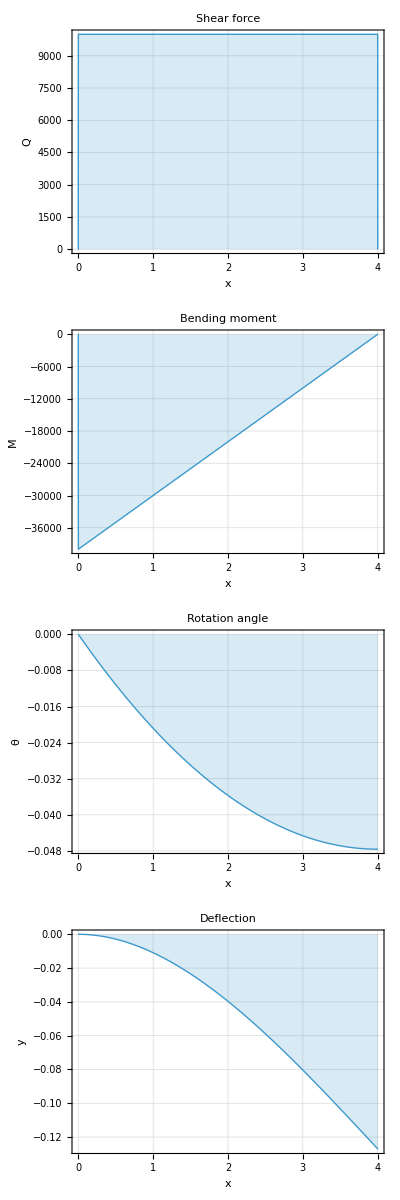

```mathematica
beamPlots[beam3SolvedValues]
```

## 4 Cantilever beam with a tip moment

### 1 Problem setup

```mathematica
ClearAll[L,EE,J,M0,x];

beam4=<|"Supports"->{<|"Type"->"FixedEnd","x"->0|>},"Loadings"->{<|"Type"->"Moment","x"->L,"Value"->M0|>},"Length"->L,"E"->EE,"J"->J,"Numbers"->{L->4,EE->210 10^9,J->8 10^-6,M0->10 10^3}|>;
```

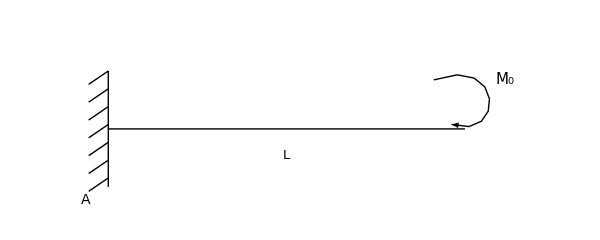

```mathematica
beamScheme4=With[{Ln=L/. beam4["Numbers"]},Graphics[{Thick,(*Beam*)Line[{{0,0},{Ln,0}}],(*Fixed support*)Line[{{0,-0.65},{0,0.65}}],Table[Line[{{-0.22,yi-0.15},{0,yi}}],{yi,-0.55,0.65,0.2}],(*Tip moment*)Arrow[BezierCurve[{{Ln-0.35,0.55},{Ln+0.45,0.85},{Ln+0.45,-0.15},{Ln-0.15,0.05}}]],(*Labels*)Text[Style[Subscript["M","0"],15,Italic],{Ln+0.45,0.55}],Text[Style["A",14,Italic],{-0.25,-0.8}],Text[Style["L",13],{Ln/2,-0.3}]},PlotRange->{{-0.6,Ln+0.9},{-1.0,1.2}},ImageSize->600]]
```

### 2 Theoretical solutions

```mathematica
theoreticalValues4=<|"ReactionForce"->0,"ReactionMoment"->-M0,"MaximumBendingMoment"->M0,"TipRotationAngle"->M0 L/(EE J),"MaximumDeflection"->M0 L^2/(2 EE J),"MaximumDeflectionPosition"->L|>;
```

```mathematica
theoreticalValues4Numerical=N[theoreticalValues4/.
beam4["Numbers"]]
```

<|ReactionForce→0.,ReactionMoment→-10000.,MaximumBendingMoment→10000.,TipRotationAngle→0.0238095,MaximumDeflection→0.047619,MaximumDeflectionPosition→4.|>

### 3 BeamSolver solution

Purely analytical solution

```mathematica
beam4Solved=beamSolve[beam4]
```

<|Supports→{<|Type→FixedEnd,x→0|>},Loadings→{<|Type→Moment,x→L,Value→M0|>,<|Type→Force,x→0,Value→0,Kind→Reaction|>,<|Type→Moment,x→0,Value→-M0,Kind→Reaction|>},Length→L,E→EE,J→J,Boundary conditions→{BeamSolver`Private`y''[0]==M0,BeamSolver`Private`y''[L]==M0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y'[0]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==M0 DiracDelta'[BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},(M0-M0 UnitStep[L])/L],BendingMoment→Function[{BeamSolver`Private`x1$},(BeamSolver`Private`x1$ (M0-M0 UnitStep[L]))/L+M0 UnitStep[BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},(((BeamSolver`Private`x1$)^2 (M0-M0 UnitStep[L]))/(2 L)+M0 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$])/(EE J)],Deflection→Function[{BeamSolver`Private`x1$},(((BeamSolver`Private`x1$)^3 (M0-M0 UnitStep[L]))/(6 L)+1/2 M0 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$])/(EE J)]|>,Numbers→{L→4,EE→210000000000,J→1/125000,M0→10000}|>

With numbers:

```mathematica
beam4SolvedValues=beamPutValues[beam4Solved]
```

<|Supports→{<|Type→FixedEnd,x→0|>},Loadings→{<|Type→Moment,x→4,Value→10000|>,<|Type→Force,x→0,Value→0,Kind→Reaction|>,<|Type→Moment,x→0,Value→-10000,Kind→Reaction|>},Length→4,E→210000000000,J→1/125000,Boundary conditions→{BeamSolver`Private`y''[0]==10000,BeamSolver`Private`y''[4]==10000,BeamSolver`Private`y[0]==0,BeamSolver`Private`y'[0]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==10000 DiracDelta'[BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},0],BendingMoment→Function[{BeamSolver`Private`x1$},10000 UnitStep[BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/168 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]],Deflection→Function[{BeamSolver`Private`x1$},1/336 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]]|>|>

```mathematica
solverValues4=N@<|"ReactionForce"->beamReactions[beam4SolvedValues][[1]]["Value"],"ReactionMoment"->beamReactions[beam4SolvedValues][[2]]["Value"],"MaximumBendingMoment"->beamMaxValue[beam4SolvedValues,"BendingMoment"]["Value"],"TipRotationAngle"->beam4SolvedValues["Solutions"]["RotationAngle"][L/. beam4["Numbers"]],"MaximumDeflection"->beamMaxValue[beam4SolvedValues,"Deflection"]["Value"],"MaximumDeflectionPosition"->beamMaxValue[beam4SolvedValues,"Deflection"]["Position"]|>
```

<|ReactionForce→0.,ReactionMoment→-10000.,MaximumBendingMoment→10000.,TipRotationAngle→0.0238095,MaximumDeflection→0.047619,MaximumDeflectionPosition→4.|>

Diagrams:

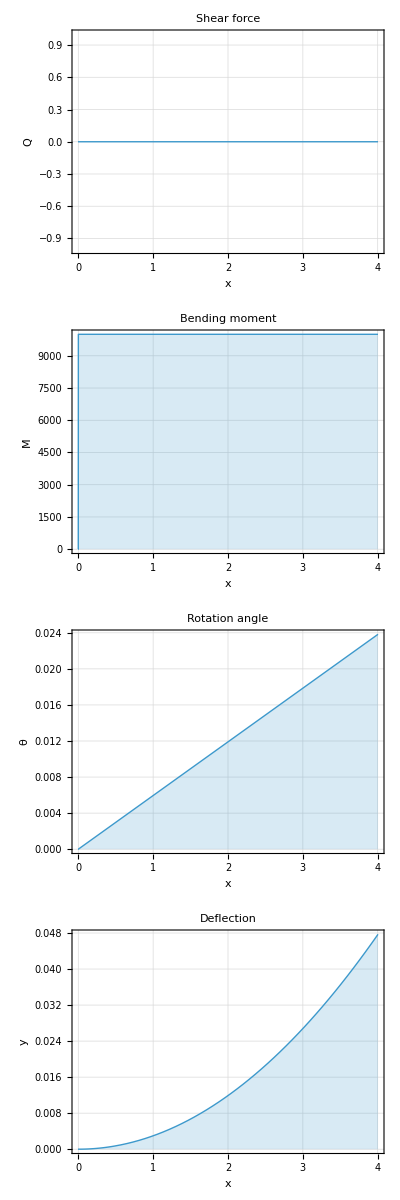

```mathematica
beamPlots[beam4SolvedValues]
```

## 5 Cantilever beam with a uniformly distributed load

### 1 Problem setup

```mathematica
ClearAll[L,EE,J,q,x];

beam5=<|"Supports"->{<|"Type"->"FixedEnd","x"->0|>},"Loadings"->{<|"Type"->"Distributed","x begin"->0,"x end"->L,"Value"->-q|>},"Length"->L,"E"->EE,"J"->J,"Numbers"->{L->4,EE->210 10^9,J->8 10^-6,q->5 10^3}|>;
```

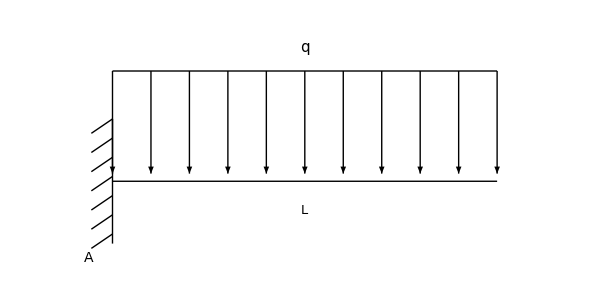

```mathematica
beamScheme5=With[{Ln=L/. beam5["Numbers"]},Graphics[{Thick,(*Beam*)Line[{{0,0},{Ln,0}}],(*Fixed support*)Line[{{0,-0.65},{0,0.65}}],Table[Line[{{-0.22,yi-0.15},{0,yi}}],{yi,-0.55,0.65,0.2}],(*Distributed-load line*)Line[{{0,1.15},{Ln,1.15}}],(*Distributed-load arrows*)Table[Arrow[{{xi,1.15},{xi,0.08}}],{xi,0,Ln,Ln/10}],(*Labels*)Text[Style["q",15,Italic],{Ln/2,1.4}],Text[Style["A",14,Italic],{-0.25,-0.8}],Text[Style["L",13],{Ln/2,-0.3}]},PlotRange->{{-0.6,Ln+0.5},{-1.0,1.6}},ImageSize->600]]
```

### 2 Theoretical solutions

```mathematica
theoreticalValues5=<|"ReactionForce"->q L,"ReactionMoment"->q L^2/2,"MaximumBendingMoment"->-q L^2/2,"MaximumBendingMomentPosition"->0,"TipRotationAngle"->-q L^3/(6 EE J),"MaximumDeflection"->-q L^4/(8 EE J),"MaximumDeflectionPosition"->L|>;
```

```mathematica
theoreticalValues5Numerical=N[theoreticalValues5/.
beam5["Numbers"]]
```

<|ReactionForce→20000.,ReactionMoment→40000.,MaximumBendingMoment→-40000.,MaximumBendingMomentPosition→0.,TipRotationAngle→-0.031746,MaximumDeflection→-0.0952381,MaximumDeflectionPosition→4.|>

### 3 BeamSolver solution

Purely analytical solution

```mathematica
beam5Solved=beamSolve[beam5]
```

<|Supports→{<|Type→FixedEnd,x→0|>},Loadings→{<|Type→Distributed,x begin→0,x end→L,Value→-q|>,<|Type→Force,x→0,Value→L q,Kind→Reaction|>,<|Type→Moment,x→0,Value→(L^2 q)/2,Kind→Reaction|>},Length→L,E→EE,J→J,Boundary conditions→{BeamSolver`Private`y''[0]==-(L^2 q)/2,BeamSolver`Private`y''[L]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y'[0]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==L q DiracDelta[BeamSolver`Private`x]-q HeavisideTheta[BeamSolver`Private`x]+q HeavisideTheta[-L+BeamSolver`Private`x]-1/2 L^2 q DiracDelta'[BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},1/2 L q UnitStep[-L]+L q UnitStep[BeamSolver`Private`x1$]-q BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]+q (-L+BeamSolver`Private`x1$) UnitStep[-L+BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},-1/2 L^2 q UnitStep[-L]+1/2 L q BeamSolver`Private`x1$ UnitStep[-L]-1/2 L^2 q UnitStep[BeamSolver`Private`x1$]+L q BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]-1/2 q (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]+1/2 q (-L+BeamSolver`Private`x1$)^2 UnitStep[-L+BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/(EE J)(1/6 L^3 q UnitStep[-L]-1/2 L^2 q BeamSolver`Private`x1$ UnitStep[-L]+1/4 L q (BeamSolver`Private`x1$)^2 UnitStep[-L]-1/2 L^2 q BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]+1/2 L q (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]-1/6 q (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$]+1/6 q (-L+BeamSolver`Private`x1$)^3 UnitStep[-L+BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/(EE J)(-1/24 L^4 q UnitStep[-L]+1/6 L^3 q BeamSolver`Private`x1$ UnitStep[-L]-1/4 L^2 q (BeamSolver`Private`x1$)^2 UnitStep[-L]+1/12 L q (BeamSolver`Private`x1$)^3 UnitStep[-L]-1/4 L^2 q (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]+1/6 L q (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$]-1/24 q (BeamSolver`Private`x1$)^4 UnitStep[BeamSolver`Private`x1$]+1/24 q (-L+BeamSolver`Private`x1$)^4 UnitStep[-L+BeamSolver`Private`x1$])]|>,Numbers→{L→4,EE→210000000000,J→1/125000,q→5000}|>

With numbers:

```mathematica
beam5SolvedValues=beamPutValues[beam5Solved]
```

<|Supports→{<|Type→FixedEnd,x→0|>},Loadings→{<|Type→Distributed,x begin→0,x end→4,Value→-5000|>,<|Type→Force,x→0,Value→20000,Kind→Reaction|>,<|Type→Moment,x→0,Value→40000,Kind→Reaction|>},Length→4,E→210000000000,J→1/125000,Boundary conditions→{BeamSolver`Private`y''[0]==-40000,BeamSolver`Private`y''[4]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y'[0]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==20000 DiracDelta[BeamSolver`Private`x]+5000 HeavisideTheta[-4+BeamSolver`Private`x]-5000 HeavisideTheta[BeamSolver`Private`x]-40000 DiracDelta'[BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},5000 (-4+BeamSolver`Private`x1$) UnitStep[-4+BeamSolver`Private`x1$]+20000 UnitStep[BeamSolver`Private`x1$]-5000 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},2500 (-4+BeamSolver`Private`x1$)^2 UnitStep[-4+BeamSolver`Private`x1$]-40000 UnitStep[BeamSolver`Private`x1$]+20000 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]-2500 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/1680000(2500/3 (-4+BeamSolver`Private`x1$)^3 UnitStep[-4+BeamSolver`Private`x1$]-40000 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]+10000 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]-2500/3 (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/1680000(625/3 (-4+BeamSolver`Private`x1$)^4 UnitStep[-4+BeamSolver`Private`x1$]-20000 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]+10000/3 (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$]-625/3 (BeamSolver`Private`x1$)^4 UnitStep[BeamSolver`Private`x1$])]|>|>

```mathematica
solverValues5=N@<|"ReactionForce"->beamReactions[beam5SolvedValues][[1]]["Value"],"ReactionMoment"->beamReactions[beam5SolvedValues][[2]]["Value"],"MaximumBendingMoment"->beamMaxValue[beam5SolvedValues,"BendingMoment"]["Value"],"MaximumBendingMomentPosition"->beamMaxValue[beam5SolvedValues,"BendingMoment"]["Position"],"TipRotationAngle"->beam5SolvedValues["Solutions"]["RotationAngle"][L/. beam5["Numbers"]],"MaximumDeflection"->beamMaxValue[beam5SolvedValues,"Deflection"]["Value"],"MaximumDeflectionPosition"->beamMaxValue[beam5SolvedValues,"Deflection"]["Position"]|>
```

<|ReactionForce→20000.,ReactionMoment→40000.,MaximumBendingMoment→-40000.,MaximumBendingMomentPosition→0.,TipRotationAngle→-0.031746,MaximumDeflection→-0.0952381,MaximumDeflectionPosition→4.|>

Diagrams:

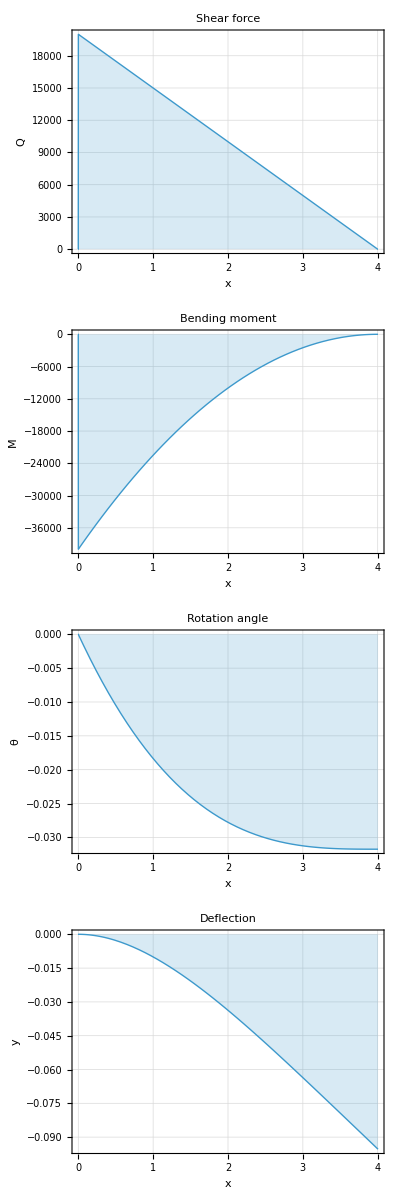

```mathematica
beamPlots[beam5SolvedValues]
```

## 6 Simply supported beam with an eccentric point load

### 1 Problem setup

```mathematica
ClearAll[L,EE,J,P,a,x];

beam6=<|"Supports"->{<|"Type"->"Pin","x"->0|>,<|"Type"->"Pin","x"->L|>},"Loadings"->{<|"Type"->"Force","x"->a,"Value"->-P|>},"Length"->L,"E"->EE,"J"->J,"Numbers"->{L->4,EE->210 10^9,J->8 10^-6,P->10 10^3,a->1.5}|>;
```

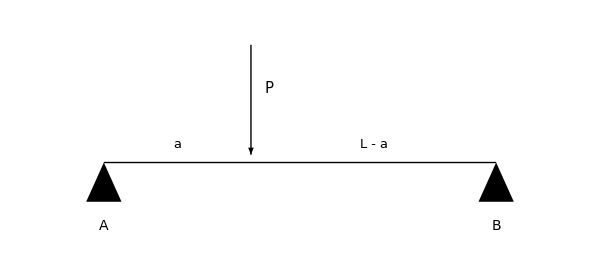

```mathematica
beamScheme6=With[{Ln=L/. beam6["Numbers"],an=a/. beam6["Numbers"]},Graphics[{Thick,(*Beam*)Line[{{0,0},{Ln,0}}],(*Supports*)Polygon[{{-0.18,-0.4},{0.18,-0.4},{0,0}}],Polygon[{{Ln-0.18,-0.4},{Ln+0.18,-0.4},{Ln,0}}],(*Point load*)Arrow[{{an,1.2},{an,0.08}}],(*Labels*)Text[Style["P",15,Italic],{an+0.18,0.75}],Text[Style["A",14,Italic],{0,-0.65}],Text[Style["B",14,Italic],{Ln,-0.65}],Text[Style["a",13,Italic],{an/2,0.18}],Text[Style["L - a",13,Italic],{(an+Ln)/2,0.18}]},PlotRange->{{-0.5,Ln+0.5},{-0.9,1.4}},ImageSize->600]]
```

### 2 Theoretical solutions

```mathematica
theoreticalValues6=<|"ReactionA"->P (L-a)/L,"ReactionB"->P a/L,"MaximumBendingMoment"->P a (L-a)/L,"MaximumBendingMomentPosition"->a,"MaximumDeflection"->-P a (L^2-a^2)^(3/2)/(9 √3 EE J L),"MaximumDeflectionPosition"->L-√((L^2-a^2)/3)|>;
```

```mathematica
theoreticalValues6Numerical=N[theoreticalValues6/.
beam6["Numbers"]]
```

<|ReactionA→6250.,ReactionB→3750.,MaximumBendingMoment→9375.,MaximumBendingMomentPosition→1.5,MaximumDeflection→-0.00730084,MaximumDeflectionPosition→1.85913|>

### 3 BeamSolver solution

Purely analytical solution

```mathematica
beam6Solved=beamSolve[beam6]
```

<|Supports→{<|Type→Pin,x→0|>,<|Type→Pin,x→L|>},Loadings→{<|Type→Force,x→a,Value→-P|>,<|Type→Force,x→0,Value→(-a P+L P)/L,Kind→Reaction|>,<|Type→Force,x→L,Value→(a P)/L,Kind→Reaction|>},Length→L,E→EE,J→J,Boundary conditions→{BeamSolver`Private`y''[0]==0,BeamSolver`Private`y''[L]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y[L]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==((-a P+L P) DiracDelta[BeamSolver`Private`x])/L-P DiracDelta[-a+BeamSolver`Private`x]+(a P DiracDelta[-L+BeamSolver`Private`x])/L,Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},(a P UnitStep[-a]-a P UnitStep[-L]+a P UnitStep[L]-L P UnitStep[L]-a P UnitStep[-a+L]+L P UnitStep[-a+L])/L+P UnitStep[BeamSolver`Private`x1$]-(a P UnitStep[BeamSolver`Private`x1$])/L-P UnitStep[-a+BeamSolver`Private`x1$]+(a P UnitStep[-L+BeamSolver`Private`x1$])/L],BendingMoment→Function[{BeamSolver`Private`x1$},-a P UnitStep[-a]+a P UnitStep[-L]+(BeamSolver`Private`x1$ (a P UnitStep[-a]-a P UnitStep[-L]+a P UnitStep[L]-L P UnitStep[L]-a P UnitStep[-a+L]+L P UnitStep[-a+L]))/L+P BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]-(a P BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$])/L-P (-a+BeamSolver`Private`x1$) UnitStep[-a+BeamSolver`Private`x1$]+(a P (-L+BeamSolver`Private`x1$) UnitStep[-L+BeamSolver`Private`x1$])/L],RotationAngle→Function[{BeamSolver`Private`x1$},1/(EE J)(BeamSolver`Private`x1$ (-a P UnitStep[-a]+a P UnitStep[-L])+((BeamSolver`Private`x1$)^2 (a P UnitStep[-a]-a P UnitStep[-L]+a P UnitStep[L]-L P UnitStep[L]-a P UnitStep[-a+L]+L P UnitStep[-a+L]))/(2 L)+(a^3 P UnitStep[-a]+2 a L^2 P UnitStep[-a]-3 a L^2 P UnitStep[-L]-a^3 P UnitStep[-a+L]+3 a^2 L P UnitStep[-a+L]-2 a L^2 P UnitStep[-a+L])/(6 L)+1/2 P (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]-(a P (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$])/(2 L)-1/2 P (-a+BeamSolver`Private`x1$)^2 UnitStep[-a+BeamSolver`Private`x1$]+(a P (-L+BeamSolver`Private`x1$)^2 UnitStep[-L+BeamSolver`Private`x1$])/(2 L))],Deflection→Function[{BeamSolver`Private`x1$},1/(EE J)(1/2 (BeamSolver`Private`x1$)^2 (-a P UnitStep[-a]+a P UnitStep[-L])+1/6 (-a^3 P UnitStep[-a]+a L^2 P UnitStep[-L])+((BeamSolver`Private`x1$)^3 (a P UnitStep[-a]-a P UnitStep[-L]+a P UnitStep[L]-L P UnitStep[L]-a P UnitStep[-a+L]+L P UnitStep[-a+L]))/(6 L)+1/(6 L)BeamSolver`Private`x1$ (a^3 P UnitStep[-a]+2 a L^2 P UnitStep[-a]-3 a L^2 P UnitStep[-L]-a^3 P UnitStep[-a+L]+3 a^2 L P UnitStep[-a+L]-2 a L^2 P UnitStep[-a+L])+1/6 P (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$]-(a P (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$])/(6 L)-1/6 P (-a+BeamSolver`Private`x1$)^3 UnitStep[-a+BeamSolver`Private`x1$]+(a P (-L+BeamSolver`Private`x1$)^3 UnitStep[-L+BeamSolver`Private`x1$])/(6 L))]|>,Numbers→{L→4,EE→210000000000,J→1/125000,P→10000,a→1.5}|>

With numbers:

```mathematica
beam6SolvedValues=beamPutValues[beam6Solved]
```

<|Supports→{<|Type→Pin,x→0|>,<|Type→Pin,x→4|>},Loadings→{<|Type→Force,x→1.5,Value→-10000|>,<|Type→Force,x→0,Value→6250.,Kind→Reaction|>,<|Type→Force,x→4,Value→3750.,Kind→Reaction|>},Length→4,E→210000000000,J→1/125000,Boundary conditions→{BeamSolver`Private`y''[0]==0,BeamSolver`Private`y''[4]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y[4]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==3750. DiracDelta[-4+BeamSolver`Private`x]-10000 DiracDelta[-1.5+BeamSolver`Private`x]+6250. DiracDelta[BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},0.+3750. UnitStep[-4+BeamSolver`Private`x1$]-10000 UnitStep[-1.5+BeamSolver`Private`x1$]+6250. UnitStep[BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},0.+3750. (-4+BeamSolver`Private`x1$) UnitStep[-4+BeamSolver`Private`x1$]-10000 (-1.5+BeamSolver`Private`x1$) UnitStep[-1.5+BeamSolver`Private`x1$]+6250. BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/1680000(-10156.3+1875. (-4+BeamSolver`Private`x1$)^2 UnitStep[-4+BeamSolver`Private`x1$]-5000 (-1.5+BeamSolver`Private`x1$)^2 UnitStep[-1.5+BeamSolver`Private`x1$]+3125. (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/1680000(0.-10156.3 BeamSolver`Private`x1$+625. (-4+BeamSolver`Private`x1$)^3 UnitStep[-4+BeamSolver`Private`x1$]-5000/3 (-1.5+BeamSolver`Private`x1$)^3 UnitStep[-1.5+BeamSolver`Private`x1$]+1041.67 (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$])]|>|>

```mathematica
solverValues6=<|"ReactionA"->beamReactions[beam6SolvedValues][[1]]["Value"],"ReactionB"->beamReactions[beam6SolvedValues][[2]]["Value"],"MaximumBendingMoment"->beamMaxValue[beam6SolvedValues,"BendingMoment"]["Value"],"MaximumBendingMomentPosition"->beamMaxValue[beam6SolvedValues,"BendingMoment"]["Position"],"MaximumDeflection"->beamMaxValue[beam6SolvedValues,"Deflection"]["Value"],"MaximumDeflectionPosition"->beamMaxValue[beam6SolvedValues,"Deflection"]["Position"]|>
```

<|ReactionA→6250.,ReactionB→3750.,MaximumBendingMoment→9375.,MaximumBendingMomentPosition→1.5,MaximumDeflection→-0.00730084,MaximumDeflectionPosition→1.85913|>

Diagrams:

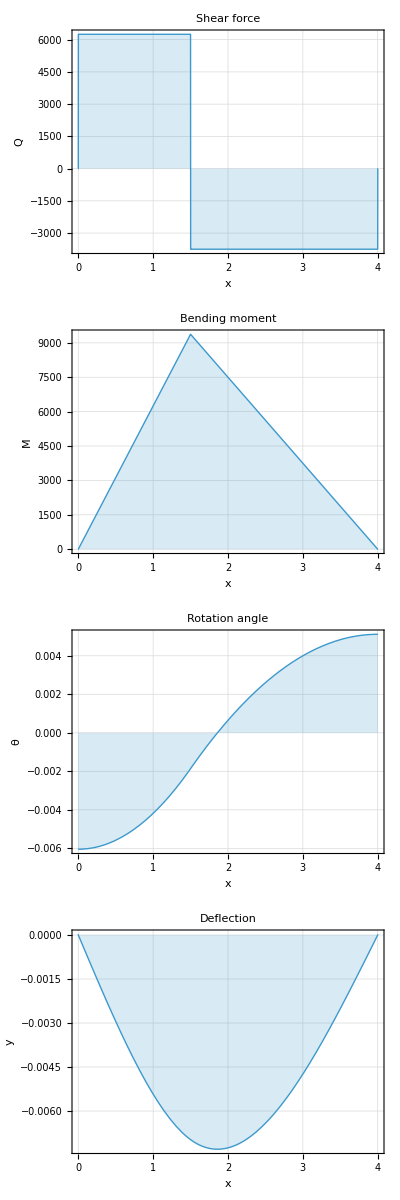

```mathematica
beamPlots[beam6SolvedValues]
```

## 7 Simply supported beam with a central concentrated moment

### 1 Problem setup

```mathematica
ClearAll[L,EE,J,M0,x];

beam7=<|"Supports"->{<|"Type"->"Pin","x"->0|>,<|"Type"->"Pin","x"->L|>},"Loadings"->{<|"Type"->"Moment","x"->L/2,"Value"->M0|>},"Length"->L,"E"->EE,"J"->J,"Numbers"->{L->4,EE->210 10^9,J->8 10^-6,M0->10 10^3}|>;
```

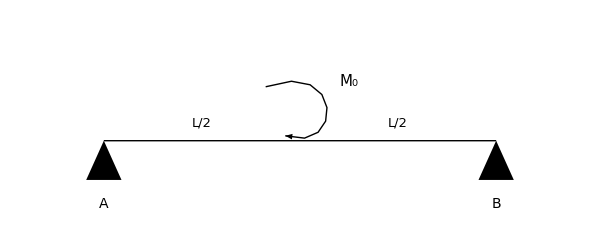

```mathematica
beamScheme7=With[{Ln=L/. beam7["Numbers"]},Graphics[{Thick,(*Beam*)Line[{{0,0},{Ln,0}}],(*Supports*)Polygon[{{-0.18,-0.4},{0.18,-0.4},{0,0}}],Polygon[{{Ln-0.18,-0.4},{Ln+0.18,-0.4},{Ln,0}}],(*Central moment*)Arrow[BezierCurve[{{Ln/2-0.35,0.55},{Ln/2+0.45,0.85},{Ln/2+0.45,-0.15},{Ln/2-0.15,0.05}}]],(*Labels*)Text[Style[Subscript["M","0"],15,Italic],{Ln/2+0.5,0.6}],Text[Style["A",14,Italic],{0,-0.65}],Text[Style["B",14,Italic],{Ln,-0.65}],Text[Style["L/2",13],{Ln/4,0.18}],Text[Style["L/2",13],{3 Ln/4,0.18}]},PlotRange->{{-0.5,Ln+0.5},{-0.9,1.2}},ImageSize->600]]
```

### 2 Theoretical solutions

```mathematica
theoreticalValues7=<|"ReactionA"->M0/L,"ReactionB"->-M0/L,"MaximumBendingMomentMagnitude"->M0/2,"MaximumDeflectionMagnitude"->M0 L^2/(72 √3 EE J),"DeflectionExtremumPosition1"->L/(2 √3),"DeflectionExtremumPosition2"->L-L/(2 √3)|>;
```

```mathematica
theoreticalValues7Numerical=N[theoreticalValues7/.
beam7["Numbers"]]
```

<|ReactionA→2500.,ReactionB→-2500.,MaximumBendingMomentMagnitude→5000.,MaximumDeflectionMagnitude→0.000763691,DeflectionExtremumPosition1→1.1547,DeflectionExtremumPosition2→2.8453|>

### 3 BeamSolver solution

Purely analytical solution

```mathematica
beam7Solved=beamSolve[beam7]
```

<|Supports→{<|Type→Pin,x→0|>,<|Type→Pin,x→L|>},Loadings→{<|Type→Moment,x→L/2,Value→M0|>,<|Type→Force,x→0,Value→M0/L,Kind→Reaction|>,<|Type→Force,x→L,Value→-M0/L,Kind→Reaction|>},Length→L,E→EE,J→J,Boundary conditions→{BeamSolver`Private`y''[0]==0,BeamSolver`Private`y''[L]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y[L]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==(M0 DiracDelta[BeamSolver`Private`x])/L-(M0 DiracDelta[-L+BeamSolver`Private`x])/L-M0 DiracDelta'[-L/2+BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},(M0 UnitStep[-L]-M0 UnitStep[-L/2]+M0 UnitStep[L/2]-M0 UnitStep[L])/L+(M0 UnitStep[BeamSolver`Private`x1$])/L-(M0 UnitStep[-L+BeamSolver`Private`x1$])/L],BendingMoment→Function[{BeamSolver`Private`x1$},-M0 UnitStep[-L]+M0 UnitStep[-L/2]+(BeamSolver`Private`x1$ (M0 UnitStep[-L]-M0 UnitStep[-L/2]+M0 UnitStep[L/2]-M0 UnitStep[L]))/L+(M0 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$])/L-(M0 (-L+BeamSolver`Private`x1$) UnitStep[-L+BeamSolver`Private`x1$])/L-M0 UnitStep[-L/2+BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/(EE J)(BeamSolver`Private`x1$ (-M0 UnitStep[-L]+M0 UnitStep[-L/2])+1/24 (12 L M0 UnitStep[-L]-11 L M0 UnitStep[-L/2]-L M0 UnitStep[L/2])+((BeamSolver`Private`x1$)^2 (M0 UnitStep[-L]-M0 UnitStep[-L/2]+M0 UnitStep[L/2]-M0 UnitStep[L]))/(2 L)+(M0 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$])/(2 L)-(M0 (-L+BeamSolver`Private`x1$)^2 UnitStep[-L+BeamSolver`Private`x1$])/(2 L)-M0 (-L/2+BeamSolver`Private`x1$) UnitStep[-L/2+BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/(EE J)(1/2 (BeamSolver`Private`x1$)^2 (-M0 UnitStep[-L]+M0 UnitStep[-L/2])+1/24 (-4 L^2 M0 UnitStep[-L]+3 L^2 M0 UnitStep[-L/2])+1/24 BeamSolver`Private`x1$ (12 L M0 UnitStep[-L]-11 L M0 UnitStep[-L/2]-L M0 UnitStep[L/2])+((BeamSolver`Private`x1$)^3 (M0 UnitStep[-L]-M0 UnitStep[-L/2]+M0 UnitStep[L/2]-M0 UnitStep[L]))/(6 L)+(M0 (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$])/(6 L)-(M0 (-L+BeamSolver`Private`x1$)^3 UnitStep[-L+BeamSolver`Private`x1$])/(6 L)-1/2 M0 (-L/2+BeamSolver`Private`x1$)^2 UnitStep[-L/2+BeamSolver`Private`x1$])]|>,Numbers→{L→4,EE→210000000000,J→1/125000,M0→10000}|>

With numbers:

```mathematica
beam7SolvedValues=beamPutValues[beam7Solved]
```

<|Supports→{<|Type→Pin,x→0|>,<|Type→Pin,x→4|>},Loadings→{<|Type→Moment,x→2,Value→10000|>,<|Type→Force,x→0,Value→2500,Kind→Reaction|>,<|Type→Force,x→4,Value→-2500,Kind→Reaction|>},Length→4,E→210000000000,J→1/125000,Boundary conditions→{BeamSolver`Private`y''[0]==0,BeamSolver`Private`y''[4]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y[4]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==-2500 DiracDelta[-4+BeamSolver`Private`x]+2500 DiracDelta[BeamSolver`Private`x]-10000 DiracDelta'[-2+BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},-2500 UnitStep[-4+BeamSolver`Private`x1$]+2500 UnitStep[BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},-2500 (-4+BeamSolver`Private`x1$) UnitStep[-4+BeamSolver`Private`x1$]-10000 UnitStep[-2+BeamSolver`Private`x1$]+2500 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/1680000(-5000/3-1250 (-4+BeamSolver`Private`x1$)^2 UnitStep[-4+BeamSolver`Private`x1$]-10000 (-2+BeamSolver`Private`x1$) UnitStep[-2+BeamSolver`Private`x1$]+1250 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/1680000(-(5000 BeamSolver`Private`x1$)/3-1250/3 (-4+BeamSolver`Private`x1$)^3 UnitStep[-4+BeamSolver`Private`x1$]-5000 (-2+BeamSolver`Private`x1$)^2 UnitStep[-2+BeamSolver`Private`x1$]+1250/3 (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$])]|>|>

```mathematica
solverValues7=<|"ReactionA"->beamReactions[beam7SolvedValues][[1]]["Value"],"ReactionB"->beamReactions[beam7SolvedValues][[2]]["Value"],"MaximumBendingMomentMagnitude"->Abs[beamMaxValue[beam7SolvedValues,"BendingMoment"]["Value"]],"MaximumDeflectionMagnitude"->Abs[beamMaxValue[beam7SolvedValues,"Deflection"]["Value"]]|>
```

<|ReactionA→2500,ReactionB→-2500,MaximumBendingMomentMagnitude→5000.,MaximumDeflectionMagnitude→0.000763691|>

Diagrams:

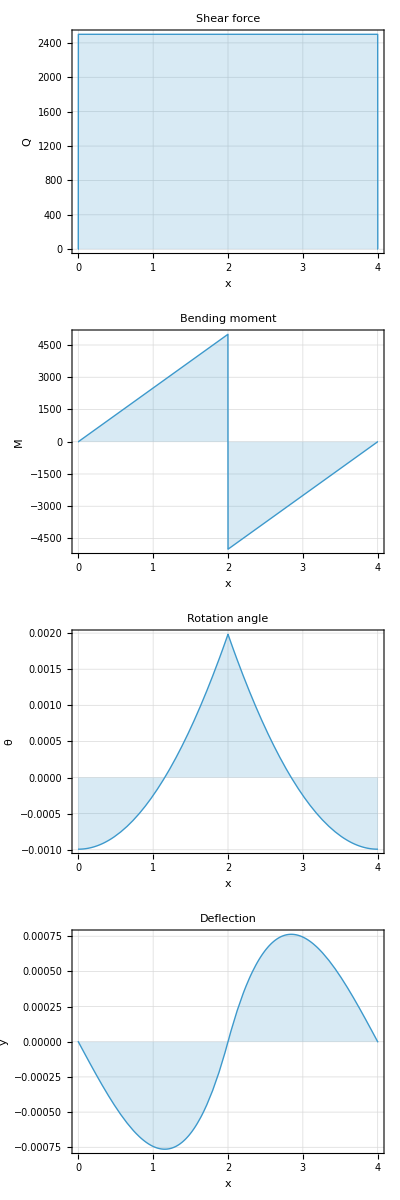

```mathematica
beamPlots[beam7SolvedValues]
```

## 8 Overhanging beam with a tip point load

### 1 Problem setup

```mathematica
ClearAll[L,EE,J,P,b,x];

beam8=<|"Supports"->{<|"Type"->"Pin","x"->0|>,<|"Type"->"Pin","x"->b|>},"Loadings"->{<|"Type"->"Force","x"->L,"Value"->-P|>},"Length"->L,"E"->EE,"J"->J,"Numbers"->{L->4,EE->210 10^9,J->8 10^-6,P->10 10^3,b->3}|>;
```

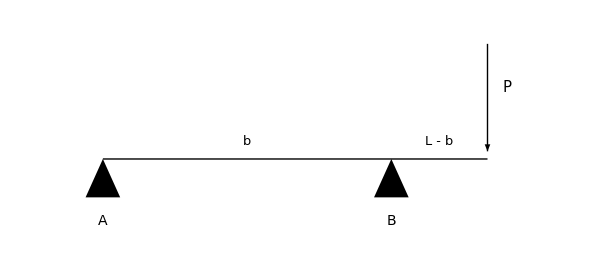

```mathematica
beamScheme8=With[{Ln=L/. beam8["Numbers"],bn=b/. beam8["Numbers"]},Graphics[{Thick,(*Beam*)Line[{{0,0},{Ln,0}}],(*Supports*)Polygon[{{-0.18,-0.4},{0.18,-0.4},{0,0}}],Polygon[{{bn-0.18,-0.4},{bn+0.18,-0.4},{bn,0}}],(*Tip load*)Arrow[{{Ln,1.2},{Ln,0.08}}],(*Labels*)Text[Style["P",15,Italic],{Ln+0.2,0.75}],Text[Style["A",14,Italic],{0,-0.65}],Text[Style["B",14,Italic],{bn,-0.65}],Text[Style["b",13,Italic],{bn/2,0.18}],Text[Style["L - b",13,Italic],{(bn+Ln)/2,0.18}]},PlotRange->{{-0.5,Ln+0.6},{-0.9,1.4}},ImageSize->600]]
```

### 2 Theoretical solutions

```mathematica
theoreticalValues8=<|"ReactionA"->-P (L-b)/b,"ReactionB"->P L/b,"MaximumBendingMoment"->-P (L-b),"MaximumBendingMomentPosition"->b,"MaximumDeflection"->-P L (L-b)^2/(3 EE J),"MaximumDeflectionPosition"->L|>;
```

```mathematica
theoreticalValues8Numerical=N[theoreticalValues8/.
beam8["Numbers"]]
```

<|ReactionA→-3333.33,ReactionB→13333.3,MaximumBendingMoment→-10000.,MaximumBendingMomentPosition→3.,MaximumDeflection→-0.00793651,MaximumDeflectionPosition→4.|>

### 3 BeamSolver solution

Purely analytical solution

```mathematica
beam8Solved=beamSolve[beam8]
```

<|Supports→{<|Type→Pin,x→0|>,<|Type→Pin,x→b|>},Loadings→{<|Type→Force,x→L,Value→-P|>,<|Type→Force,x→0,Value→((b-L) P)/b,Kind→Reaction|>,<|Type→Force,x→b,Value→(L P)/b,Kind→Reaction|>},Length→L,E→EE,J→J,Boundary conditions→{BeamSolver`Private`y''[0]==0,BeamSolver`Private`y''[L]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y[b]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==((b-L) P DiracDelta[BeamSolver`Private`x])/b+(L P DiracDelta[-b+BeamSolver`Private`x])/b-P DiracDelta[-L+BeamSolver`Private`x],Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},(-b P UnitStep[-b]+b P UnitStep[-L]-b P UnitStep[L]+L P UnitStep[L]+b P UnitStep[-b+L]-L P UnitStep[-b+L])/b+P UnitStep[BeamSolver`Private`x1$]-(L P UnitStep[BeamSolver`Private`x1$])/b+(L P UnitStep[-b+BeamSolver`Private`x1$])/b-P UnitStep[-L+BeamSolver`Private`x1$]],BendingMoment→Function[{BeamSolver`Private`x1$},L P UnitStep[-b]-L P UnitStep[-L]+(BeamSolver`Private`x1$ (-b P UnitStep[-b]+b P UnitStep[-L]-b P UnitStep[L]+L P UnitStep[L]+b P UnitStep[-b+L]-L P UnitStep[-b+L]))/b+P BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]-(L P BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$])/b+(L P (-b+BeamSolver`Private`x1$) UnitStep[-b+BeamSolver`Private`x1$])/b-P (-L+BeamSolver`Private`x1$) UnitStep[-L+BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/(EE J)(BeamSolver`Private`x1$ (L P UnitStep[-b]-L P UnitStep[-L])+((BeamSolver`Private`x1$)^2 (-b P UnitStep[-b]+b P UnitStep[-L]-b P UnitStep[L]+L P UnitStep[L]+b P UnitStep[-b+L]-L P UnitStep[-b+L]))/(2 b)+1/(6 b)(b^3 P UnitStep[-b]-4 b^2 L P UnitStep[-b]-b^3 P UnitStep[b]+b^2 L P UnitStep[b]+b^3 P UnitStep[b-L]-3 b^2 L P UnitStep[b-L]+3 b L^2 P UnitStep[b-L]-L^3 P UnitStep[b-L]-b^3 P UnitStep[-L]+3 b^2 L P UnitStep[-L]+L^3 P UnitStep[-L]+b^3 P UnitStep[L]-b^2 L P UnitStep[L]-b^3 P UnitStep[-b+L]+b^2 L P UnitStep[-b+L])+1/2 P (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$]-(L P (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$])/(2 b)+(L P (-b+BeamSolver`Private`x1$)^2 UnitStep[-b+BeamSolver`Private`x1$])/(2 b)-1/2 P (-L+BeamSolver`Private`x1$)^2 UnitStep[-L+BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/(EE J)(1/2 (BeamSolver`Private`x1$)^2 (L P UnitStep[-b]-L P UnitStep[-L])+1/6 (b^2 L P UnitStep[-b]-L^3 P UnitStep[-L])+((BeamSolver`Private`x1$)^3 (-b P UnitStep[-b]+b P UnitStep[-L]-b P UnitStep[L]+L P UnitStep[L]+b P UnitStep[-b+L]-L P UnitStep[-b+L]))/(6 b)+1/(6 b)BeamSolver`Private`x1$ (b^3 P UnitStep[-b]-4 b^2 L P UnitStep[-b]-b^3 P UnitStep[b]+b^2 L P UnitStep[b]+b^3 P UnitStep[b-L]-3 b^2 L P UnitStep[b-L]+3 b L^2 P UnitStep[b-L]-L^3 P UnitStep[b-L]-b^3 P UnitStep[-L]+3 b^2 L P UnitStep[-L]+L^3 P UnitStep[-L]+b^3 P UnitStep[L]-b^2 L P UnitStep[L]-b^3 P UnitStep[-b+L]+b^2 L P UnitStep[-b+L])+1/6 P (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$]-(L P (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$])/(6 b)+(L P (-b+BeamSolver`Private`x1$)^3 UnitStep[-b+BeamSolver`Private`x1$])/(6 b)-1/6 P (-L+BeamSolver`Private`x1$)^3 UnitStep[-L+BeamSolver`Private`x1$])]|>,Numbers→{L→4,EE→210000000000,J→1/125000,P→10000,b→3}|>

With numbers:

```mathematica
beam8SolvedValues=beamPutValues[beam8Solved]
```

<|Supports→{<|Type→Pin,x→0|>,<|Type→Pin,x→3|>},Loadings→{<|Type→Force,x→4,Value→-10000|>,<|Type→Force,x→0,Value→-10000/3,Kind→Reaction|>,<|Type→Force,x→3,Value→40000/3,Kind→Reaction|>},Length→4,E→210000000000,J→1/125000,Boundary conditions→{BeamSolver`Private`y''[0]==0,BeamSolver`Private`y''[4]==0,BeamSolver`Private`y[0]==0,BeamSolver`Private`y[3]==0},Equation→(BeamSolver`Private`y)^(4)[BeamSolver`Private`x]==-10000 DiracDelta[-4+BeamSolver`Private`x]+40000/3 DiracDelta[-3+BeamSolver`Private`x]-(10000 DiracDelta[BeamSolver`Private`x])/3,Solutions→<|ShearForce→Function[{BeamSolver`Private`x1$},-10000 UnitStep[-4+BeamSolver`Private`x1$]+40000/3 UnitStep[-3+BeamSolver`Private`x1$]-(10000 UnitStep[BeamSolver`Private`x1$])/3],BendingMoment→Function[{BeamSolver`Private`x1$},-10000 (-4+BeamSolver`Private`x1$) UnitStep[-4+BeamSolver`Private`x1$]+40000/3 (-3+BeamSolver`Private`x1$) UnitStep[-3+BeamSolver`Private`x1$]-10000/3 BeamSolver`Private`x1$ UnitStep[BeamSolver`Private`x1$]],RotationAngle→Function[{BeamSolver`Private`x1$},1/1680000(5000-5000 (-4+BeamSolver`Private`x1$)^2 UnitStep[-4+BeamSolver`Private`x1$]+20000/3 (-3+BeamSolver`Private`x1$)^2 UnitStep[-3+BeamSolver`Private`x1$]-5000/3 (BeamSolver`Private`x1$)^2 UnitStep[BeamSolver`Private`x1$])],Deflection→Function[{BeamSolver`Private`x1$},1/1680000(5000 BeamSolver`Private`x1$-5000/3 (-4+BeamSolver`Private`x1$)^3 UnitStep[-4+BeamSolver`Private`x1$]+20000/9 (-3+BeamSolver`Private`x1$)^3 UnitStep[-3+BeamSolver`Private`x1$]-5000/9 (BeamSolver`Private`x1$)^3 UnitStep[BeamSolver`Private`x1$])]|>|>

```mathematica
solverValues8=N@<|"ReactionA"->beamReactions[beam8SolvedValues][[1]]["Value"],"ReactionB"->beamReactions[beam8SolvedValues][[2]]["Value"],"MaximumBendingMoment"->beamMaxValue[beam8SolvedValues,"BendingMoment"]["Value"],"MaximumBendingMomentPosition"->beamMaxValue[beam8SolvedValues,"BendingMoment"]["Position"],"MaximumDeflection"->beamMaxValue[beam8SolvedValues,"Deflection"]["Value"],"MaximumDeflectionPosition"->beamMaxValue[beam8SolvedValues,"Deflection"]["Position"]|>
```

<|ReactionA→-3333.33,ReactionB→13333.3,MaximumBendingMoment→-10000.,MaximumBendingMomentPosition→3.,MaximumDeflection→-0.00793651,MaximumDeflectionPosition→4.|>

Diagrams:

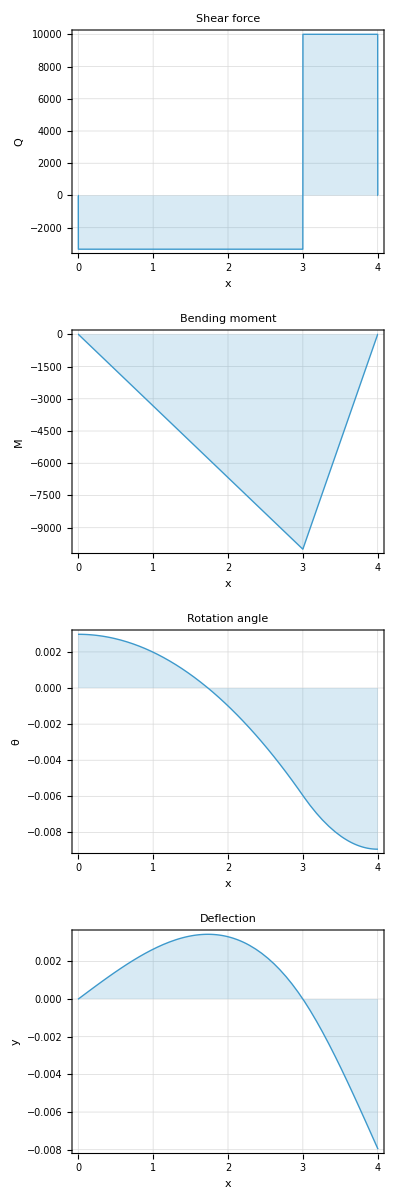

```mathematica
beamPlots[beam8SolvedValues]
```

## A more complicated beam

## 1 Problem setup

```mathematica
ClearAll[a,b,c,q,M,P,xP,xM,x];

myBeam=<|"Supports"->{<|"Type"->"Pin","x"->a|>,<|"Type"->"Pin","x"->a+b+c|>},"Loadings"->{<|"Type"->"Force","x"->xP,"Value"->-P|>,<|"Type"->"Moment","x"->xM,"Value"->-M|>,<|"Type"->"Distributed","x begin"->0,"x end"->a,"Value"->-2 q|>,<|"Type"->"Distributed","x begin"->a+b,"x end"->a+b+c,"Value"->q|>},"Length"->a+b+c,"E"->1,"J"->1,"Numbers"->{a->2.,b->1.6,c->2.4,q->4.,M->12.,P->10.,xP->3.6,xM->2.}|>;
```

-Graphics-

## 2 BeamSolver solution

```mathematica
myBeamSolved=beamSolve[myBeam];
```

```mathematica
myBeamSolvedValues=beamPutValues[myBeamSolved];
```

```mathematica
beamReactions[myBeamSolvedValues]
```

{<|Type→Force,x→2.,Value→20.12,Kind→Reaction|>,<|Type→Force,x→6.,Value→-3.72,Kind→Reaction|>}

```mathematica
beamMaxValue[myBeamSolvedValues,"ShearForce"]
```

<|Quantity→ShearForce,Value→-16.,Position→2.|>

```mathematica
beamMaxValue[myBeamSolvedValues,"BendingMoment"]
```

<|Quantity→BendingMoment,Value→-16.,Position→2.|>

```mathematica
beamMaxValue[myBeamSolvedValues,"RotationAngle"]
```

<|Quantity→RotationAngle,Value→12.0576,Position→0|>

```mathematica
beamMaxValue[myBeamSolvedValues,"Deflection"]
```

<|Quantity→Deflection,Value→-18.7819,Position→0|>

For the overhang:

```mathematica
beamInitialParameters[myBeamSolvedValues]
```

<|RotationAngle→12.0576,Deflection→-18.7819|>

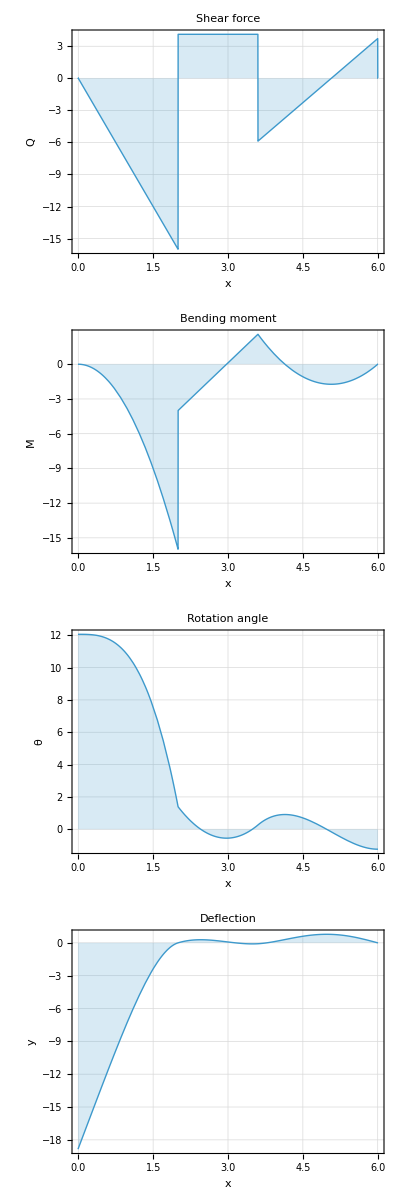

```mathematica
beamPlots[myBeamSolvedValues]
```

## Key feature: make use of analytical solutions

Let’s make the diagrams interactive: move the force P and the moment M along the beam. To animate the diagrams, we will use Manipulate. Because our deflection solution is analytical, Manipulate is nice and fast:

```mathematica
ClearAll@supp
supp[x_,size_]:=With[{hCoeff=100},Triangle[{{x-size,-hCoeff size},{x,0},{x+size,-hCoeff size}}]]

ClearAll[pointLoad]
Options[pointLoad]={"ArrowLength"->55,"ArrowheadSize"->0.04,"Style"->Directive[Red,Thickness[0.008]],"Label"->None,"LabelOffset"->{14,0},"LabelStyle"->Directive[Red,14,Italic]};
pointLoad[f_,xP_?NumericQ,force_?NumericQ,opts:OptionsPattern[]]:=Module[{direction,arrowLength,tip,tail,label,labelOffset,labelPosition},If[Chop[force]==0,Return[{}]];
direction=Sign[force];
arrowLength=OptionValue["ArrowLength"];
label=OptionValue["Label"];
labelOffset=OptionValue["LabelOffset"];
tip={xP,f[xP]};
tail=Offset[{0,direction arrowLength},tip];
labelPosition=Offset[{labelOffset[[1]],direction arrowLength/2+labelOffset[[2]]},tip];
{OptionValue["Style"],Arrowheads[OptionValue["ArrowheadSize"]],Arrow[{tail,tip}],If[label===None,Nothing,Text[Style[label,OptionValue["LabelStyle"]],labelPosition]]}];

ClearAll@uniformDistributedLoad
Options[uniformDistributedLoad]={"NumberOfArrows"->9,"ArrowLength"->24,"ArrowheadSize"->0.025,"ShowLoadLine"->True,"Style"->Directive[Black,AbsoluteThickness[1.6]],"Label"->None,"LabelStyle"->Directive[Black,14,Italic],"LabelGap"->15};
uniformDistributedLoad[f_,{x1_?NumericQ,x2_?NumericQ},q_?NumericQ,opts:OptionsPattern[]]:=Module[{n,arrowLength,xs,beamPoints,loadPoints,label,labelPoint,xMid},If[Chop[q]==0||x2<=x1,Return[{}]];
n=Max[2,Round@OptionValue["NumberOfArrows"]];
arrowLength=OptionValue["ArrowLength"];
label=OptionValue["Label"];
xs=Subdivide[x1,x2,n-1];
beamPoints=({#,f[#]}&)/@xs;
loadPoints=(Offset[{0,Sign[q] arrowLength},#]&)/@beamPoints;
xMid=(x1+x2)/2;
labelPoint=Offset[{0,Sign[q] (arrowLength+OptionValue["LabelGap"])},{xMid,f[xMid]}];
{OptionValue["Style"],If[TrueQ@OptionValue["ShowLoadLine"],Line[loadPoints],Nothing],Arrowheads[OptionValue["ArrowheadSize"]],MapThread[Arrow[{#1,#2}]&,{loadPoints,beamPoints}],If[label===None,Nothing,Text[Style[label,OptionValue["LabelStyle"]],labelPoint]]}];

ClearAll@beamMoment
Options[beamMoment]={"Direction"->Automatic,"Offset"->{0,32},"Size"->48,"SweepAngle"->3 Pi/2,"StartAngle"->3 Pi/4,"Samples"->50,"ArrowheadSize"->0.16,"Style"->Directive[Blue,AbsoluteThickness[1.8]],"Label"->None};
beamMoment[f_,xM_?NumericQ,moment_?NumericQ,opts:OptionsPattern[]]:=Module[{direction,startAngle,endAngle,angles,momentPoints,label,momentGraphic},If[Chop[moment]==0,Return[{}]];
direction=Replace[OptionValue["Direction"],{Automatic:>Sign[moment],"CCW"->1,"CW"->-1}];
startAngle=OptionValue["StartAngle"];
endAngle=startAngle+direction OptionValue["SweepAngle"];
angles=Subdivide[startAngle,endAngle,Max[12,Round@OptionValue["Samples"]]];
momentPoints=({Cos[#],Sin[#]}&)/@angles;
label=OptionValue["Label"];
momentGraphic=Graphics[{OptionValue["Style"],Arrowheads[OptionValue["ArrowheadSize"]],Arrow[momentPoints],Line[{{0,0},{Cos[angles[[1]]],Sin[angles[[1]]]}}]},PlotRange->{{-1.25,1.25},{-1.25,1.25}},ImagePadding->0,Background->None];
{Inset[momentGraphic,Offset[OptionValue["Offset"],{xM,f[xM]}],Center,Offset[OptionValue["Size"]]],If[label===None,Nothing,Text[Style[label,14,Italic],Offset[{OptionValue["Offset"][[1]]+OptionValue["Size"]/10,OptionValue["Offset"][[2]]+OptionValue["Size"]/7},{xM,f[xM]}],{0,-1}]]}];
```

```mathematica
fixedRules=DeleteCases[DeleteCases[myBeam["Numbers"],HoldPattern[xP->_]],HoldPattern[xM->_]];
{an,bn,cn,Ln}={a,b,c,a+b+c}/. fixedRules;
```

```mathematica
Manipulate[
Module[{shearForceExpression,bendingMomentExpression,rotationAngleExpression,deflectionExpression,f,fR,fB,fS},
{shearForceExpression,bendingMomentExpression,rotationAngleExpression,deflectionExpression}=(myBeamSolved["Solutions"][#][x]/.
DeleteCases[DeleteCases[myBeam["Numbers"],HoldPattern[xP->_]],HoldPattern[xM->_]]/.
{xP->xPP,xM->xMM})&/@{"ShearForce","BendingMoment","RotationAngle","Deflection"};
f=Function[{xx},Evaluate[deflectionExpression/. x->xx]];
fR=Function[{xx},Evaluate[rotationAngleExpression/. x->xx]];
fB=Function[{xx},Evaluate[bendingMomentExpression/. x->xx]];
fS=Function[{xx},Evaluate[shearForceExpression/. x->xx]];
Column[{
Plot[Evaluate[fS[x]],{x,0,Ln},PlotRange->Full(*PlotRange->{Automatic,{-30,20}}*),PerformanceGoal->"Quality",FrameLabel->{None,"Shear force V = EIv'''"},Exclusions->None,ImageSize->400,AspectRatio->1/4,Frame->True,Filling->Axis,ImagePadding->{{45, 10}, {15, 10}},Epilog->{{Red,Dashed,Line[{{xPP,-200},{xPP,200}}]},{Blue,Dashed,Line[{{xMM,-200},{xMM,200}}]}},LabelStyle->9],

Plot[Evaluate[fB[x]],{x,0,Ln},PlotRange->Full(*PlotRange->{Automatic,{-35,5}}*),PerformanceGoal->"Quality",FrameLabel->{None,"Bending moment M = EIv''"},Exclusions->None,ImageSize->400,AspectRatio->1/4,Frame->True,Filling->Axis,ImagePadding->{{45, 10}, {15, 20}},Epilog->{{Red,Dashed,Line[{{xPP,-200},{xPP,200}}]},{Blue,Dashed,Line[{{xMM,-200},{xMM,200}}]}},LabelStyle->9],

Plot[Evaluate[fR[x]],{x,0,Ln},PlotRange->Full(*PlotRange->{Automatic,{-40,75}}*),PerformanceGoal->"Quality",FrameLabel->{None,"Rotation angle θ = v'"},ImageSize->400,AspectRatio->1/4,Frame->True,Filling->Axis,ImagePadding->{{45, 10}, {15, 5}},Epilog->{{Red,Dashed,Line[{{xPP,-200},{xPP,200}}]},{Blue,Dashed,Line[{{xMM,-200},{xMM,200}}]}},LabelStyle->9],

Plot[Evaluate[f[x]],{x,0,Ln},PlotRange->{Automatic,{-120,48}},Epilog->{pointLoad[f,xPP,1,"Label"->"P","LabelOffset"->{10,15},"ArrowLength"->30],uniformDistributedLoad[f,{0,an},1,"NumberOfArrows"->7,"ArrowLength"->22,"Label"->"2q"],
uniformDistributedLoad[f,{an+bn,Ln},-1,"NumberOfArrows"->8,"ArrowLength"->20,"Label"->"q"],
beamMoment[f,xMM,1,"Offset"->{0,0},"Size"->80,"ArrowheadSize"->0.2,"Label"->Style["M",Blue],"Direction"->"CW"],supp[an,0.1],supp[Ln,0.1],{Red,Dashed,Line[{{xPP,-200},{xPP,200}}]},{Blue,Dashed,Line[{{xMM,-200},{xMM,200}}]}},PerformanceGoal->"Quality",FrameLabel->{None,"Deflection v"},ImageSize->400,PlotStyle->Thickness[0.01],Frame->True,Filling->Axis,ImagePadding->{{45, 10}, {15, 5}},LabelStyle->9,AspectRatio->1/2]
}]],
{{xPP,xP/. myBeam["Numbers"],Subscript[x,P]},0,Ln,Appearance->"Open"},
{{xMM,xM/. myBeam["Numbers"],Subscript[x,M]},0,Ln,Appearance->"Open"},
TrackedSymbols:>{xPP,xMM},SaveDefinitions->False]
```